# The Surface Code at Circuit Level

## The distance-3 surface code under CNOT and readout errors, computed with the QEC layer

Nine data qubits on a 3×3 grid carry one logical qubit in the distance-3 surface code. Its eight checks, four of X type and four of Z type, each act on two or four neighboring qubits. One round of check measurement is made by a circuit in which every CNOT fails with probability pC and every readout with probability pM. How likely is a decoder to lose the logical qubit, and is every single fault still corrected?

Each step below is one call to the QEC layer: the code, its extraction circuit, the faults, and the exact logical error rate as a polynomial in pC and pM. The last section goes past one round and past distance 3. Every timed step prints its wall time in seconds.

## Loading

```mathematica
$repo = Quiet @ Check[ParentDirectory[NotebookDirectory[], 3], "/Users/mauriceengelhard/Documents/REPOS/QuantumFramework"];
PacletDirectoryLoad[FileNameJoin[{$repo, "QuantumFramework"}]];
Needs["Wolfram`QuantumFramework`"];
Get[FileNameJoin[{$repo, "OngoingProjects", "QEC", "QECCore", "QECCore.wl"}]];
Needs["Wolfram`QuantumFramework`QEC`"];
```

## The code and its extraction circuit

QECCode["Surface"[3]] is the code of the question. Its parameters [[n, k, d]], its eight checks, and the order in which each check's CNOTs touch its data qubits (X checks row by row, Z checks column by column):

```mathematica
code = QECCode["Surface"[3]];
{code["Parameters"], code["Generators"], code["CheckOrder"]}
```

{{9,1,3},{IXXIIIIII,XXIXXIIII,IIIIXXIXX,IIIIIIXXI,ZIIZIIIII,IZZIZZIII,IIIZZIZZI,IIIIIZIIZ},{{2,3},{1,2,4,5},{5,6,8,9},{7,8},{1,4},{2,5,3,6},{4,7,5,8},{6,9}}}

Each check has its own ancilla, qubits 10 to 17, prepared in |0⟩. For an X check its data qubits are rotated by H, CNOTs copy their parity into the ancilla in the order above, the rotations are undone and the ancilla is read. The lattice is drawn from the code's own checks; the circuit is the code's "SyndromeCircuit", whose instructions QuantumCircuitOperator takes as they are:

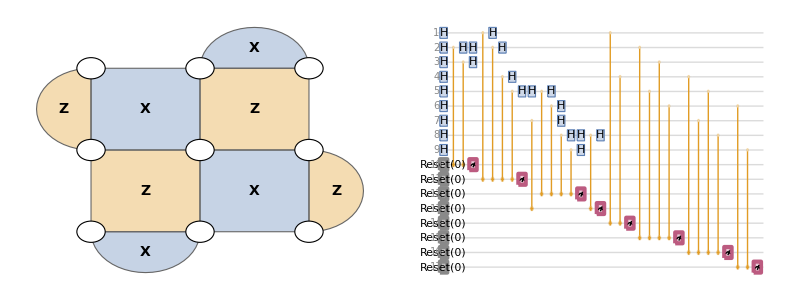

```mathematica
surfChecks = code["Generators"];
surfOrder = code["CheckOrder"];
surfXCheckQ = StringContainsQ["X"];
surfPos[q_] := {Mod[q - 1, 3], -Quotient[q - 1, 3]};
surfOut[qs_] := With[{v = Cross[Subtract @@ (surfPos /@ qs)]}, If[v . (Mean[surfPos /@ qs] - {1, -1}) > 0, v, -v]];
surfFace[qs_] := With[{c = Mean[surfPos /@ qs]}, If[Length[qs] == 4, Polygon[SortBy[surfPos /@ qs, ArcTan @@ (# - c) &]],
    Polygon[Table[c + 0.5 RotationMatrix[a] . surfOut[qs], {a, -Pi/2, Pi/2, Pi/24}]]]];
surfLattice = Graphics[{
    MapThread[Function[{qs, check}, {EdgeForm[GrayLevel[0.4]], FaceForm[Opacity[0.35, If[surfXCheckQ[check], ColorData[97][1], ColorData[97][2]]]], surfFace[qs],
        Text[Style[If[surfXCheckQ[check], "X", "Z"], 14, Bold], Mean[surfPos /@ qs] + If[Length[qs] == 2, 0.25 surfOut[qs], {0, 0}]]}], {surfOrder, surfChecks}],
    {EdgeForm[Black], White, Disk[surfPos[#], 0.13], Text[Style[#, 11], surfPos[#]]} & /@ Range[9]}, ImageSize -> 240];
Grid[{{surfLattice, QuantumCircuitOperator[code["SyndromeCircuit"]["Instructions"]]["Diagram"]}}, Spacings -> 4, Alignment -> Center]
```

## The faults

After each CNOT one of the 15 two-qubit Paulis other than the identity strikes, each with probability pC/15, and each ancilla readout is flipped with probability pM; one-qubit gates and waiting qubits do not err. The round is followed by a perfect measurement of all eight checks and of the logical operators. A detector is a check's reading in the round, or its change at that final measurement: both are 0 when nothing goes wrong.

QECDetectorModel carries every fault through the circuit at once, each one a bit of the same wide integers, as Stim's frame simulator does, and records the detectors it fires and the logical operators it flips. Faults that fire nothing and flip nothing are left out:

```mathematica
noise = QECNoiseModel["Circuit"[<|"TwoQubit" -> pC, "Measurement" -> pM|>]];
{tModel, dem} = AbsoluteTiming[QECDetectorModel[code, noise, 1]];
{tModel, dem["Faults"], dem["Detectors"], dem["Observables"]}
```

{0.012775,352,16,2}

352 faults (24 CNOTs × 15 Paulis and 8 readouts, less the 16 that do nothing), 16 detectors, and both logical operators. Counted by how many detectors they fire and by how many of them flip a logical operator:

```mathematica
With[{rows = Transpose[{dem["DetectorMatrix"], dem["ObservableMatrix"]}]},
 Grid[Transpose[Prepend[KeyValueMap[{#1, Length[#2], Count[#2[[All, 2]], {___, 1, ___}]} &, KeySort[GroupBy[rows, Total[First[#]] &]]],
    {"detectors fired", "faults", "of which flip a logical"}]], Frame -> All, FrameStyle -> GrayLevel[0.8], Background -> {{GrayLevel[0.93], None}}]]
```

detectors fired | 1 | 2 | 3 | 4
faults | 72 | 144 | 88 | 48
of which flip a logical | 32 | 38 | 36 | 34

## Two decoders, exactly

The first decoder knows the pattern of every single fault, undoes that fault, and counts any other pattern as a failure; it is QECLogicalErrorRate's default for a detector model. The second is maximum likelihood: for every pattern of the 16 detectors it applies the logical correction that is most probable given that pattern, over all combinations of faults, not only pairs. No decoder that reads these detectors does better. Its table is chosen at pC = pM = 1/1000 and then used at every rate. Both rates are exact polynomials in pC and pM:

```mathematica
{tSingle, single} = AbsoluteTiming[QECLogicalErrorRate[code, noise, "Rounds" -> 1]];
{tML, ml} = AbsoluteTiming[QECLogicalErrorRate[code, noise, "Rounds" -> 1, "Decoder" -> {"MaximumLikelihood", 1/1000}]];
{tSingle, tML}
```

{0.145189,0.205621}

Their leading terms, and where each crosses PL = p when pC = pM = p:

```mathematica
surfLead = Expand[Normal[Series[# /. {pC -> t pC, pM -> t pM}, {t, 0, 2}]] /. t -> 1] & /@ {single, ml}
```

{(48326 pC^2)/225+(2213 pC pM)/15+28 pM^2,(2438 pC^2)/45+(pC pM)/5}

```mathematica
surfCross = First[SolveValues[(# /. {pC -> p, pM -> p}) == p && 0 < p < 1/10, p, Reals]] & /@ {single, ml};
N[surfCross]
```

{0.00269019,0.0204563}

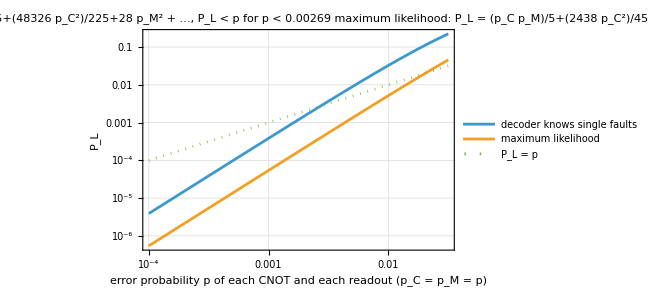

```mathematica
surfPlot = LogLogPlot[Evaluate[Append[{single, ml} /. {pC -> p, pM -> p}, p]], {p, 10^-4, 10^-1.5}, PlotStyle -> {Automatic, Automatic, Dotted}, Frame -> True, GridLines -> Automatic,
   GridLinesStyle -> Directive[GrayLevel[0.8], Dashed], FrameLabel -> {Row[{"error probability p of each CNOT and each readout  (", Subscript["p", "C"], " = ", Subscript["p", "M"], " = p)"}], Subscript["P", "L"]}, ImageSize -> 480,
   PlotLegends -> Placed[{"decoder knows single faults", "maximum likelihood", Row[{Subscript["P", "L"], " = p"}]}, Below],
   PlotLabel -> Column[MapThread[Row[{#1, ":  ", Subscript["P", "L"], " = ", TraditionalForm[#2 /. {pC -> Subscript["p", "C"], pM -> Subscript["p", "M"]}], " + …,   ", Subscript["P", "L"], " < p  for  p < ", NumberForm[N[#3], 3]}] &,
      {{"single faults", "maximum likelihood"}, surfLead, surfCross}], Alignment -> Center]]
```

Neither rate has a linear term: every single fault, in a CNOT or in a readout, is corrected. With readout errors alone the first decoder fails exactly when two or more of the eight readings are wrong, while maximum likelihood recognizes every two and every three wrong readings and first fails at four:

```mathematica
{Simplify[(single /. pC -> 0) - (1 - (1 - pM)^8 - 8 pM (1 - pM)^7)], Factor[ml /. pC -> 0]}
```

{0,pM^4 (2-3 pM+pM^2+pM^4)}

The single-fault polynomial is the one surface-code.nb computes. Maximum likelihood has the leading terms of that notebook's second decoder, which knew every pair of faults, (2438/45) pC^2 + pC pM/5, and is lower still, since it also uses the combinations of three and more. The two rates at p = 1/1000 and p = 1/100:

```mathematica
Grid[Prepend[Table[{p0, N[single /. {pC -> p0, pM -> p0}], N[ml /. {pC -> p0, pM -> p0}]}, {p0, {1/1000, 1/100}}], {"p", "single faults", "maximum likelihood"}], Frame -> All]
```

p | single faults | maximum likelihood
1/1000 | 0.000383286 | 0.0000541175
1/100 | 0.0325963 | 0.0051727

## How the rate is computed

Faults at different locations are independent, and their effects, bit patterns over the 16 detectors and the two logical operators, add bit by bit. In the Walsh–Hadamard transform each location then contributes one factor, f(k) = 1 - 2 ∑ p_r over the outcomes r that are odd under k, and a decoder that fails on the patterns W fails with probability 2^-N ∑_k W^(k) ∏ f(k). At a CNOT either none or exactly eight of the fifteen Paulis are odd under k, so its factor is 1 or 1 - 16 pC/15; a readout contributes 1 or 1 - 2 pM.

QECLogicalErrorRate does this for any detector model. W^ is the transform of a 0/1 vector, an exact integer vector computed in machine arithmetic; the k are grouped by how many of each factor they collect, so the symbolic part is a short sum of monomials. Maximum likelihood comes from the same machinery run the other way: with numeric rates the product of factors is the transform of the whole distribution, and one inverse transform gives the probability of every pattern. The exact route covers up to $QECExactDetectorLimit patterns:

```mathematica
$QECExactDetectorLimit == 2^24
```

True

## Past one round and past distance 3

More rounds multiply the detectors. "Basis" -> "Z" keeps a memory in one basis, the Z-bar observable and the detectors of the Z checks; on a CSS code that is an exact marginal of the full model, and it halves the bits. Rounds 1 to 4 of the distance-3 code, exactly, under pC = pM = p, with the time each takes and the leading term:

```mathematica
Grid[Prepend[Table[
   With[{n = QECNoiseModel["Circuit"[<|"TwoQubit" -> p, "Measurement" -> p|>]]},
    Module[{t, r},
     {t, r} = AbsoluteTiming[QECLogicalErrorRate[code, n, "Rounds" -> rounds, "Basis" -> "Z", "Decoder" -> {"MaximumLikelihood", 1/1000}]];
     {rounds, Round[t, 0.01], Normal[Series[r, {p, 0, 2}]]}]],
   {rounds, 1, 4}], {"rounds", "seconds", "leading term"}], Frame -> All]
```

rounds | seconds | leading term
1 | 0.04 | (2932 p^2)/75
2 | 0.21 | (31132 p^2)/225
3 | 0.62 | (6348 p^2)/25
4 | 2.42 | (83108 p^2)/225

One round of the distance-5 code in one basis is 25 bits, 2^25 patterns, past the default limit, which is raised for this one call. The leading power is p^3, as distance 5 requires (this step needs about 3 GB of memory):

```mathematica
{t5, d5} = AbsoluteTiming[Block[{$QECExactDetectorLimit = 2^25},
    QECLogicalErrorRate[QECCode["Surface"[5]], QECNoiseModel["Circuit"[<|"TwoQubit" -> p, "Measurement" -> p|>]],
     "Rounds" -> 1, "Basis" -> "Z", "Decoder" -> {"MaximumLikelihood", 1/1000}]]];
{t5, Normal[Series[d5, {p, 0, 3}]]}
```

{15.7767,(42320 p^3)/27}

Past the exact route the rate is sampled. The sampled rate agrees with the exact one where both exist:

```mathematica
SeedRandom[2026];
With[{n = QECNoiseModel["Circuit"[<|"TwoQubit" -> 1/50, "Measurement" -> 1/50|>]]},
 {QECLogicalErrorRate[code, n, 50000, "Rounds" -> 1, "Basis" -> "Z", "Decoder" -> "MaximumLikelihood"],
  N[QECLogicalErrorRate[code, n, "Rounds" -> 1, "Basis" -> "Z", "Decoder" -> "MaximumLikelihood"]]}]
```

{0.01274,0.0133324}

The standard memory experiment, d noisy rounds of the distance-d code, decoded by matching, 20000 shots each at p = 3/1000. The time includes building the detector model:

```mathematica
SeedRandom[2026];
Grid[Prepend[Table[
   With[{n = QECNoiseModel["Circuit"[<|"TwoQubit" -> 3/1000, "Measurement" -> 3/1000|>]]},
    Module[{t, r},
     {t, r} = AbsoluteTiming[QECLogicalErrorRate[QECCode["Surface"[d]], n, 20000, "Rounds" -> d, "Basis" -> "Z", "Decoder" -> "Matching"]];
     {d, Round[t, 0.1], r}]],
   {d, {3, 5, 7}}], {"d = rounds", "seconds", "logical error rate per experiment"}], Frame -> All]
```

d = rounds | seconds | logical error rate per experiment
3 | 0.2 | 0.0021
5 | 3. | 0.0007
7 | 15.8 | 0.00025

The logical error rate falls with the distance at this p, which is below the threshold of the circuit.